First we input the story as text:

```mathematica
corpus:="Discoveries covering sensations of an inner, physical or spiritual punch of reality of realisation can be far reading and transformative but will always impact an individualís life and those around. The Entire History of you & Rainbows End both experience impacts affecting the relationship between friends and loved ones reconsidering their beliefs and values. 

In rainbows End Gladis transforms Dollyís life as well as her own, impacting their cultural status and discoveries of the world around them by Dollys rape experience, Gladis care has grown significantly for the protection and well-being of Dolly. As Errol is introduced as a spark of Dollys attraction and appearance catches Errols attention, Gladis is yet to neither welcome nor except Errol as he as so foreign being an outsider, making it harder for them to discover their love for each other . As far reaching as an unexpected flood washing away their only home with all of their belonging including their encyclopaedia (their only form of education) having new discovers made as they were ìforced to leaveî.

Gladis discovers her inner confidence & courage to raise her family in the environment & access to any education for Dolly to work, has transformed her values , attitudes and beliefs towards the community & her own personal life considering her protect and ability to look after her family. Cultural disadvantages such as power and status has made Gladis a stronger and wiser mother creating a role model overview.

Errols surprising impact and discovery on Dollys life places a huge amount of pressure to consider caring for someone as much as someone caring for herself. Errol as connected new information with previous experiences & cultural assumptions about Dolly has transformed Dollys view on outsiders and her value of expectance has made Dolly a much stronger and sophisticated person than she used to be. Dollys life style & racial considerations make it harder for her to get employed and as advice through experiences from Gladis and Errol help to transform and discover more about Dolly than she knew herself could become true. "

tCells:={TextCell["Escher - Belonging","Subtitle"]};
AppendTo[tCells,TextCell["Number of words: "<>ToString[WordCount[corpus]],"Text"]];
words:=ToLowerCase[StringSplit[corpus, Except[WordCharacter]..]];
sentences:=TextSentences[corpus];
AppendTo[tCells,TextCell["Number of distinct words: "<>ToString[CountDistinct[words]],"Text"]];
AppendTo[tCells,TextCell["Vocab density: "<>ToString[N[CountDistinct[words]/Length[words],3]],"Text"]];
trimmedWords:=DeleteStopwords[words];
AppendTo[tCells,TextCell["Vocab density, without stop words: "<>ToString[N[CountDistinct[trimmedWords]/Length[trimmedWords],3]],"Text"]];
AppendTo[tCells,TextCell["The 20 most commonly used words:","Text"]];
AppendTo[tCells,Take[WordCounts[DeleteStopwords[corpus]],20]];
AppendTo[tCells,TextCell["Density of adjectives: "<>ToString[N[Length[Intersection[WordList["Adjective"],trimmedWords]]/Length[trimmedWords],3]],"Text"]];
AppendTo[tCells,TextCell["The most common punctuation: ", "Text"]];
AppendTo[tCells,CharacterCounts[ToString[StringCases[corpus, PunctuationCharacter]]]];
sentenceLengths:=Length/@StringSplit/@sentences;
AppendTo[tCells,Histogram[sentenceLengths, PlotLabel->"Sentence length: Total distribution"]];
AppendTo[tCells,ListStepPlot[sentenceLengths, PlotLabel->"Sentence length: Over course of text"]];
nb:=CreateDocument[tCells]
NotebookPrint[nb,"Escher - Belonging Analysis.pdf"]
```

```mathematica
nb
```

p4qq3_shm195FrontEndObject[LinkObject["p4qq3_shm", 3, 1]]195Untitled-127

### Analysis

Number of words: 377

Number of distinct words: 189

Vocab density: 0.495

Vocab density, without stop words: 0.667

The 20 most commonly used words:

<|Macbeth→15,ambition→9,play→8,Lady→4,king→4,witches→3,Thane→3,prophecy→3,force→3,driving→3,Act→3,uses→2,throughout→2,Shakespeare→2,resolved→2,reaction→2,power→2,later→2,Glamis→2,Foul→2|>

Density of adjectives: 0.164

The most common punctuation:

<|,→96, →66,.→19,’→6,“→4,”→4,/→2,‘→1,}→1,{→1,!→1|>

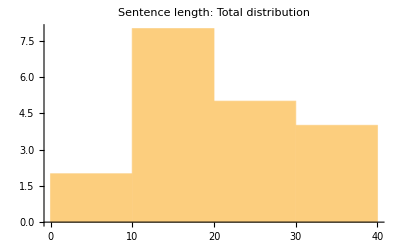

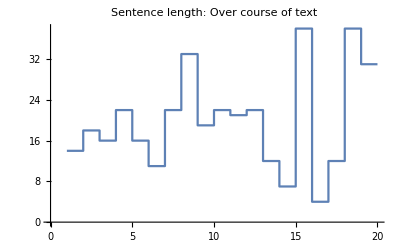

```mathematica
TextCell["Number of words: "<>ToString[WordCount[corpus]],"Text"]

words:=ToLowerCase[StringSplit[corpus, Except[WordCharacter]..]]
sentences:=TextSentences[corpus]

TextCell["Number of distinct words: "<>ToString[CountDistinct[words]],"Text"]

TextCell["Vocab density: "<>ToString[N[CountDistinct[words]/Length[words],3]],"Text"]
trimmedWords:=DeleteStopwords[words];

TextCell["Vocab density, without stop words: "<>ToString[N[CountDistinct[trimmedWords]/Length[trimmedWords],3]],"Text"]
TextCell["The 20 most commonly used words:","Text"]
Take[WordCounts[DeleteStopwords[corpus]],20]
TextCell["Density of adjectives: "<>ToString[N[Length[Intersection[WordList["Adjective"],trimmedWords]]/Length[trimmedWords],3]],"Text"]
TextCell["The most common punctuation: ", "Text"]
CharacterCounts[ToString[StringCases[corpus, PunctuationCharacter]]]
sentenceLengths:=Length/@StringSplit/@sentences;
Histogram[sentenceLengths, PlotLabel->"Sentence length: Total distribution"]
ListStepPlot[sentenceLengths, PlotLabel->"Sentence length: Over course of text"]
```

Using the two above, we can create a measure of the vocabularly variety, by dividing the distinct words by the total words, we get a measure from 0 to 1 of the word variation. 1 being every single word is different.

```mathematica
WhitespaceCharacter
```

<|,→96, →66,.→19,’→6,“→4,”→4,/→2,‘→1,}→1,{→1,!→1|>

We can also remove words such as “then”, “this”, “and”, known as stop words, and then repeat the vocab density calculation. This should be a larger number more often than not.

Vocab density, without stop words:

0.666667

```mathematica
Print["The 20 most commonly used words:"];Take[WordCounts[DeleteStopwords[corpus]],20]
```

The 20 most commonly used words:

<|Macbeth→15,ambition→9,play→8,Lady→4,king→4,witches→3,Thane→3,prophecy→3,force→3,driving→3,Act→3,uses→2,throughout→2,Shakespeare→2,resolved→2,reaction→2,power→2,later→2,Glamis→2,Foul→2|>

We can also look at the density of certain types of words, for example:

Note that the above example may count words as adjectives when they are not being used as such in a sentence, however it should be good enough for a rough measure.

### Sentence length

We can also look at the sentece length throughout the text

```mathematica
sentenceLengths:=Length/@StringSplit/@sentences;
Histogram[sentenceLengths, PlotLabel->"Sentence length: Total distribution"]
```

-Graphics-

```mathematica
ListStepPlot[sentenceLengths, PlotLabel->"Sentence length: Over course of text"]
```

-Graphics-

We can also look at the mean of the absolute value of the second differences of the sentence length as a measure of the variability of the sentence lengths throughout the text. This gives us a sense of how much short sentences follow long ones (higher being more variation)

17.7059

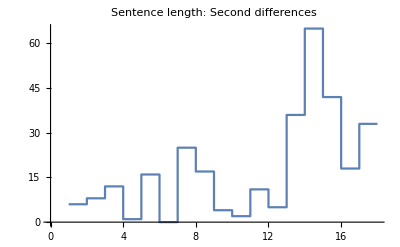

```mathematica
Mean[Abs/@Differences[sentenceLengths,2]]//N
ListStepPlot[Interpolation[Abs/@Differences[sentenceLengths,2]], PlotLabel->"Sentence length: Second differences"]
```

We can also drill down into the individual sentence structure itself

```mathematica
TextStructure[sentences[[4]]]
```

It
Pronoun
Noun Phrase  is
Verb  then
Adverb
Adverb Phrase    developed
Verb  throughout
Preposition    the
Determinerplay
Noun
Noun Phrase  with
Preposition  Lady
Proper NounMacbeth
Proper Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Verb Phrase,
Punctuationand
Conjunction  brutally
Adverb
Adverb Phrase  resolved
Verb  in
Preposition  Act
Proper Noun5
Numeral
Noun Phrase
Prepositional Phrase,
Punctuation  with
Preposition      Macbeth
Proper Noun's
Missing[KeyAbsent,Nothing]
Noun Phrasehead
Noun
Noun Phrase  on
Preposition  a
Determinerstake
Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
corpus
```

corpus

```mathematica
sentenceLengths
```

{14,18,16,22,16,11,22,33,19,22,21,22,12,7,38,4,12,38,31}

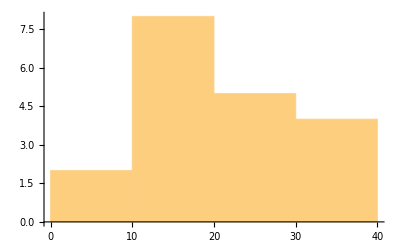
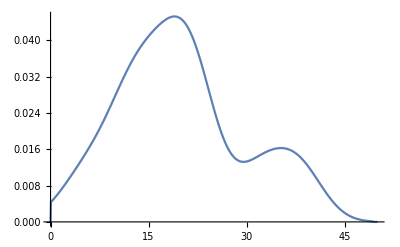

```mathematica
Overlay[{Histogram[sentenceLengths],SmoothHistogram[sentenceLengths,PlotRange->{{0,50},All}]}]
```

```mathematica
tCells
```

{Number of words: 377}